# T=0 Effective Potential

```mathematica
ClearAll["Global`*"];
```

```mathematica
S[A_,μS_,h_]:=A/(2 μS^2)h^2;
V0[λ_,A_,μH_,μS_,h_]:=1/4 λ h^4-1/2 μH^2 h^2+1/2 μS^2 S[A,μS,h]^2-1/2 A S[A,μS,h] h^2;
V02d[λ_,A_,μH_,μS_,h_,S_]:=1/4 λ h^4-1/2 μH^2 h^2+1/2 μS^2 S^2-1/2 A S h^2;
treevev[λ_,A_,μH_,μS_]:=μH μS √(1/(2λ μS^2-A^2));
```

```mathematica
g=0.65;
gY=0.36;
yt=0.9945;
Q=150;
mh=125.;
v=174.;
```

```mathematica
mW[h_]:=1/4 g^2 h^2;
mZ[h_]:=1/4(g^2+gY^2)h^2;
mt[h_]:=1/2 yt^2 h^2;
mX[λ_,A_,μH_,μS_,h_]:=-μH^2-A S[A,μS,h]+λ h^2;
mX2d[λ_,A_,μH_,μS_,h_,S_]:=-μH^2-A S+λ h^2;
sqrt2d[λ_,A_,μH_,μS_,h_,S_]:=√(A^2(4 h^2+ S^2)+2A S(μH^2+μS^2-3λ h^2)+(μH^2+μS^2-3λ h^2)^2);
sqrt[λ_,A_,μH_,μS_,h_]:=√(A^2(4 h^2+ S[A,μS,h]^2)+2A S[A,μS,h](μH^2+μS^2-3λ h^2)+(μH^2+μS^2-3λ h^2)^2);
mH[λ_,A_,μH_,μS_,h_]:=1/2(-μH^2+μS^2-A S[A,μS,h]+3λ h^2+sqrt[λ,A,μH,μS,h]);
mH2d[λ_,A_,μH_,μS_,h_,S_]:=1/2(-μH^2+μS^2-A S+3λ h^2+sqrt2d[λ,A,μH,μS,h,S]);
mS[λ_,A_,μH_,μS_,h_]:=1/2(-μH^2+μS^2-A S[A,μS,h]+3λ h^2-sqrt[λ,A,μH,μS,h]);
mS2d[λ_,A_,μH_,μS_,h_,S_]:=1/2(-μH^2+μS^2-A S+3λ h^2-sqrt2d[λ,A,μH,μS,h,S]);
VCW[λ_,A_,μH_,μS_,h_]:=1/(64 π^2)(6 mW[h]^2(Log[mW[h]/Q^2]-5./6)+3 mZ[h]^2(Log[mZ[h]/Q^2]-5./6)+mH[λ,A,μH,μS,h]^2(Log[Abs[mH[λ,A,μH,μS,h]]/Q^2]-3./2)+3 mX[λ,A,μH,μS,h]^2(Log[Abs[mX[λ,A,μH,μS,h]]/Q^2]-3./2)-12 mt[h]^2(Log[mt[h]/Q^2]-3./2));
VCW2d[λ_,A_,μH_,μS_,h_,S_]:=1/(64 π^2)(6 mW[h]^2(Log[mW[h]/Q^2]-5/6)+3 mZ[h]^2(Log[mZ[h]/Q^2]-5/6)+mH2d[λ,A,μH,μS,h,S]^2(Log[Abs[mH2d[λ,A,μH,μS,h,S]]/Q^2]-3/2)+3 mX2d[λ,A,μH,μS,h,S]^2(Log[Abs[mX2d[λ,A,μH,μS,h,S]]/Q^2]-3/2)-12 mt[h]^2(Log[mt[h]/Q^2]-3/2));
V0T[λ_,A_,μH_,μS_,h_]:=V0[λ,A,μH,μS,h]+VCW[λ,A,μH,μS,h]-(V0[λ,A,μH,μS,10^-3]+VCW[λ,A,μH,μS,10^-3]);
V0T2d[λ_,A_,μH_,μS_,h_,S_]:=V02d[λ,A,μH,μS,h,S]+VCW2d[λ,A,μH,μS,h,S]-(V02d[λ,A,μH,μS,10^-3,10^-3]+VCW2d[λ,A,μH,μS,10^-3,10^-3]);
```

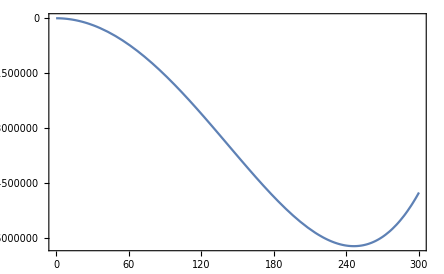

```mathematica
Plot[{V0[0.125293,10.6204,20.2598,21.8138,h]},{h,0,300}]
```

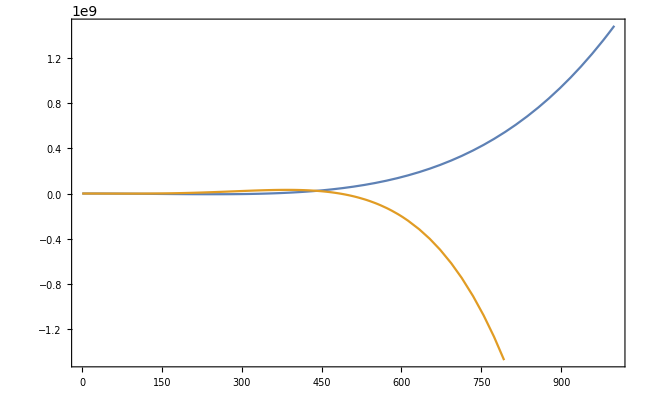

```mathematica
Plot[{V0[0.125299,10.6204,20.2598,21.8138,h],V0[0.125299,10.6204,20.2598,21.8138,h]+VCW[0.125299,10.6204,20.2598,21.8138,h]},{h,0,1000}]
```

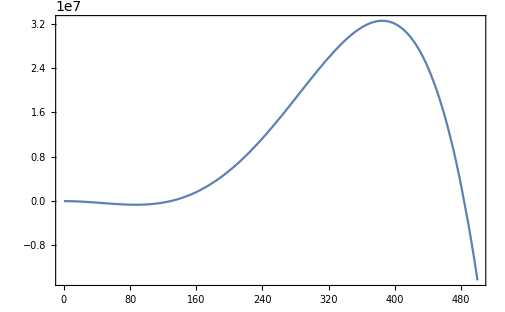

```mathematica
Plot[{V0[0.125299,10.6204,20.2598,21.8138,h]+VCW[0.125299,10.6204,20.2598,21.8138,h]},{h,0,500}]
```

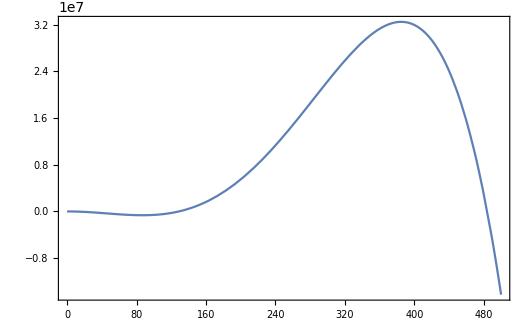

```mathematica
Plot[V0T2d[0.125299,10.6204,20.2598,21.8138,h,S[10.6204,21.8138,h]],{h,0,500}]
```

```mathematica
Plot3D[{V0T2d[0.125299,10.6204,20.2598,21.8138,h,S]},{h,0,500},{S,0,3000}]
```

-Graphics3D-

```mathematica
FindMinimum[V0T[0.125299,10.6204,20.2598,21.8138,h],h]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{-648783.,{h→86.6867}}

```mathematica
FindMinimum[V0T2d[0.125299,10.6204,20.2598,21.8138,h,S],{h,S}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{-648783.,{h→86.6866,S→83.8824}}

```mathematica
μH2[mS_,sinθ_]:=(mh^2 mS^2)/(2(sinθ^2 mh^2+(1-sinθ^2)mS^2));
μS2[mS_,sinθ_]:=sinθ^2 mh^2+(1-sinθ^2)mS^2;
A2[mS_,sinθ_]:=((mh^2-mS^2)^2 sinθ^2(1-sinθ^2))/(2 v^2);
λ[mS_,sinθ_]:=((1-sinθ^2)mh^2+sinθ^2 mS^2)/(4 v^2);
```

```mathematica
√μH2[5,0.17]
```

20.2598

```mathematica
√μS2[5,0.17]
```

21.8138

```mathematica
√A2[5,0.17]
```

10.6204

```mathematica
λ[5,0.17]
```

0.125299

```mathematica
λeff[λ_,A_,μS_]:=λ-A^2/(2 μS^2);
```

```mathematica
λeff[0.125299,10.6204,21.8138]
```

0.00677969

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
ND[V0T2d[0.125299,10.6204,20.2598,21.8138,60,S],S,40]
```

-200.987

```mathematica
ND[V0T2d[0.125299,10.6204,20.2598,21.8138,h,40.],h,60]
```

-9791.28

```mathematica
V0T2d[0.125299,10.6204,20.2598,21.8138,60,40]
```

-492723.

```mathematica
mW[500]
mZ[500]
mH2d[0.125299,10.6204,20.2598,21.8138,500,1000]
mS2d[0.125299,10.6204,20.2598,21.8138,500,1000]
mX2d[0.125299,10.6204,20.2598,21.8138,500,1000]
```

26406.3

34506.3

83283.9

135.317

20293.9

```mathematica
VCW2d[0.125299,10.6204,20.2598,21.8138,500,1000]
```

-7.11563×10^7

```mathematica
V02d[0.125299,10.6204,20.2598,21.8138,500,1000]
```

8.1686×10^8

```mathematica
SetDirectory[NotebookDirectory[]]
<<anybubble.m
<<powell.m
Options[FindBubble]
```

/Users/isaac/Dropbox/Research_Project/2022-1-SFOPT_light_singlet/02-Analysis/phase_transition

{Verbose→False,SpaceTimeDimension→4,StartAnalyticFraction→1/100,EndAnalyticFraction→1/100,MaxIntervalGrowth→30,MaxReadjustments→20,InitialProfilePoints→{},PowellVerbosity→1,MaxIterations→500,AccuracyGoal→Automatic,WorkingPrecision→MachinePrecision}

```mathematica
S[10.6204,21.8138,700]
```

5468.2

```mathematica
VCW[0.125299,10.6204,20.2598,21.8138,500]
```

-6.88988×10^7

```mathematica
V0T[0.125299,10.6204,20.2598,21.8138,1]
```

-205.973

```mathematica
V0[0.125299,10.6204,20.2598,21.8138,0]+VCW[0.125299,10.6204,20.2598,21.8138,0]
```

Indeterminate

```mathematica
V0T[0.125299,10.6204,20.2598,21.8138,500]
```

-1.42671×10^7

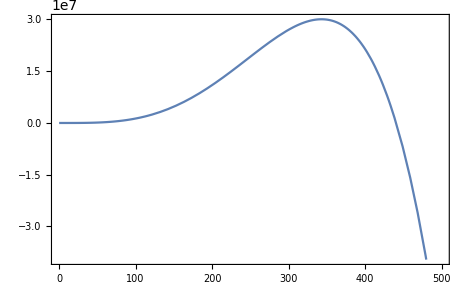

```mathematica
Plot[VCW[0.125299,10.6204,20.2598,21.8138,h],{h,0,500}]
```

```mathematica
V0T[0.125299,10.6204,20.2598,21.8138,1]
```

-205.973

```mathematica
VCW[0.125299,10.6204,20.2598,21.8138,87]+V0[0.125299,10.6204,20.2598,21.8138,87]
```

-655080.

```mathematica
mW[300]
```

9506.25

```mathematica
mH[0.125299,10.6204,20.2598,21.8138,300]
```

23200.2

```mathematica
V0[0.125299,10.6204,20.2598,21.8138,500]
```

5.46253×10^7